```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Temp\fastm\res

```mathematica
n=1000;
```

```mathematica
SolVM={Flatten[Import["sol-0-1dot1","Table"]][[1;;n]],Flatten[Import["sol-0-1dot1","Table"]][[n+2;;2n+1]]};
```

Part::take: Cannot take positions 1 through 1000 in {0.341763,0.224339,0.106953,-0.0103242,-0.127534,-0.244889,-0.362844,-0.482091,-0.603678,-0.729116,«192»}.

Part::take: Cannot take positions 1002 through 2001 in {0.341763,0.224339,0.106953,-0.0103242,-0.127534,-0.244889,-0.362844,-0.482091,-0.603678,-0.729116,«192»}.

```mathematica
SolUnique=Flatten[Import["sol-0","Table"]][[1;;n]];
```

Part::take: Cannot take positions 1 through 1000 in {-0.0628005,-0.188151,-0.312763,-0.436147,-0.557795,-0.677235,-0.794035,-0.907685,-1.01773,-1.12378,«91»}.

```mathematica
SolOld=Flatten[Import["gamRes.txt","Table"]][[;;-2]];
Sol0=Flatten[Import["gamRes0.txt","Table"]][[;;-2]];
Sol1=Flatten[Import["gamRes1.txt","Table"]][[;;-2]];
```

```mathematica
SolNumPNL[t_?NumberQ,Sol_]:=Module[{xt,yt,rt,q,St},
 q=1;While[t>q+1,q++];
rt=t-q;
Sol[[q]](*+Sol[[n+q]]*(rt-1/2)*)
]
```

```mathematica
SolNumPNLLIN[t_?NumberQ,Sol_]:=Module[{xt,yt,rt,q,St},
 q=1;While[t>q+1,q++];
rt=t-q;
Sol[[q]]+Sol[[n+q]]*(rt-1/2)
]
```

```mathematica
len=Norm[1/2{Cos[2 π/100],Sin[2 π/100]}-{1/2,0.0}]
```

0.0314108

```mathematica
Sol0;
```

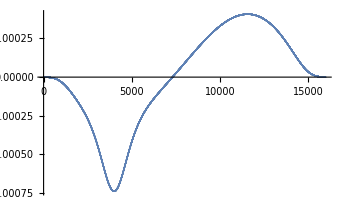

```mathematica
ListPlot[Sol0[[1;;16000]]]
```

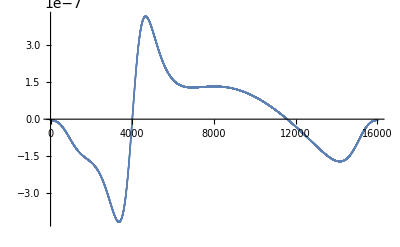

```mathematica
ListPlot[Sol0[[16001;;32000]]]
```

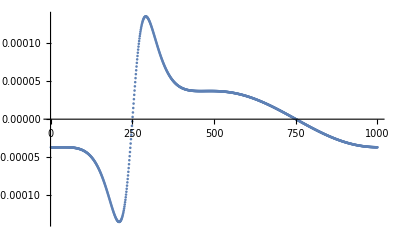

-Graphics-

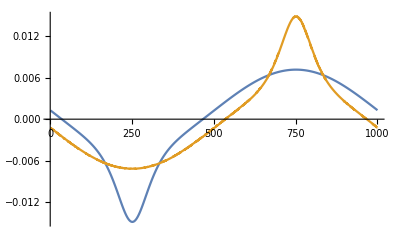

```mathematica
Plot[{SolNumPNLLIN[t,Sol0],SolNumPNL[t,Sol1]},{t,1,1000},PlotPoints->1000]
```

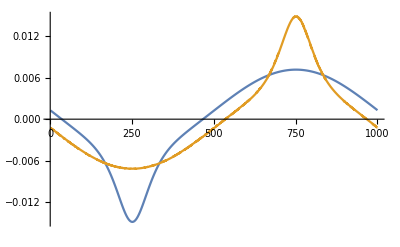

-Graphics-

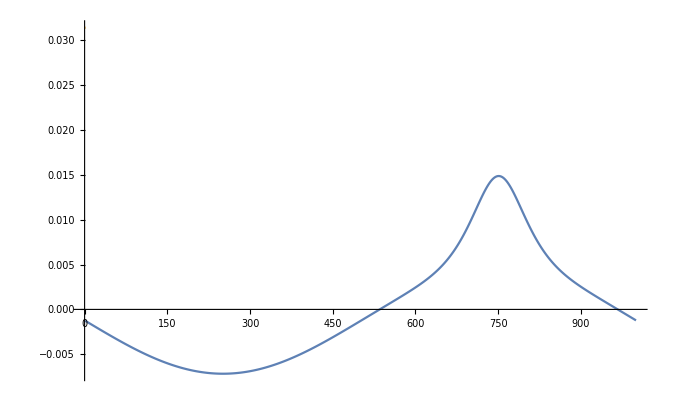

```mathematica
Plot[{SolNumPNLLIN[t,Sol1],SolNumPNL[t,len SolVM[[2]]]},{t,1,1000},PlotPoints->1000]
```

```mathematica
(64000 Log[2,64000])/(16000Log[2,16000])//N
```

4.57283

```mathematica
(16000 16 2)
```

512000

```mathematica
π/8000.
```

0.000392699

```mathematica
exact=Flatten[Import["ExactCircle8000-linear-0.txt","Table"]];
```

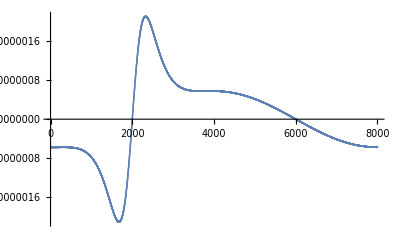

```mathematica
ListPlot[(exact)[[8001;;16000]],PlotRange->All]
```

```mathematica
res=Flatten[Import["gamRes0.txt","Table"]];
```

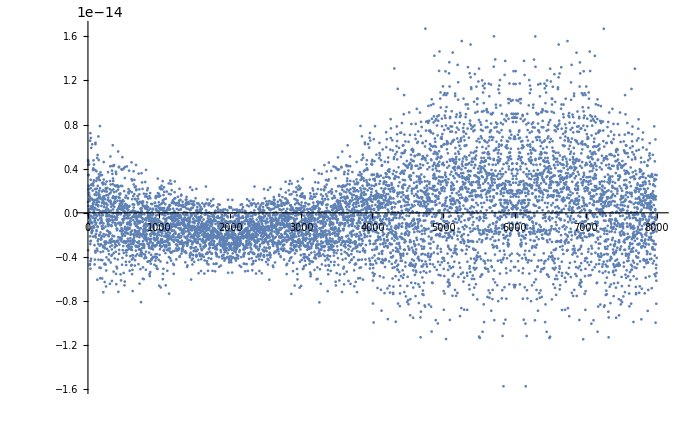

```mathematica
ListPlot[(res-exact)[[1;;8000]],PlotRange->All]
```

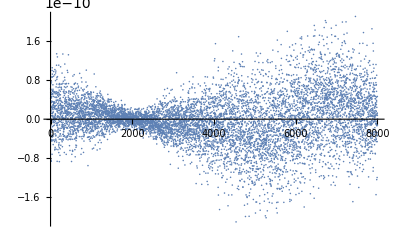

```mathematica
ListPlot[(res-exact)[[8001;;16000]],PlotRange->All]
```

```mathematica
π/8000.
```

0.000392699

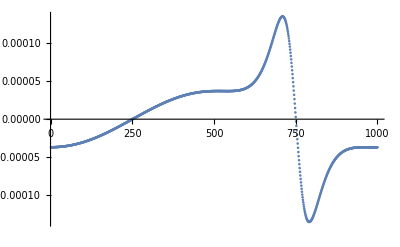

```mathematica
ListPlot[res[[1001;;2000]],PlotRange->All]
```